```mathematica
a=Import["~/MSLoop_HNGN277_SN2_Blk2_Operation_P&T-220413B.CSV"];
```

```mathematica
a[[1]]
```

{MSLoop_HNGN277_ SN2_Blk2_Operation start  2022-04-13 20:04:16.856697}

```mathematica
a[[2]]
```

{2022-04-13 20:04:18.002513,P_Volt= 3.341883,Tc= [458.1875,457.938,389.,543.375,101.5,20.625,19.9375,19.875,20.25,20.3125],maxTc_meas=543.375,iL=[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0]}

```mathematica
Length[a]
```

33670

```mathematica
b=Table[a[[2,i]],{i,3,12}]
```

{Tc= [458.1875,457.938,389.,543.375,101.5,20.625,19.9375,19.875,20.25,20.3125]}

```mathematica
Length[b]
```

10

```mathematica
b[[1]]
```

Tc= [458.1875

```mathematica
StringReplace[b[[1]],"Tc= ["->""]
```

458.1875

```mathematica
StringReplace[b[[10]],"]"->""]
```

20.3125

```mathematica
c=Table[Table[a[[i,k]],{k,3,12}],{i,2,Length[a]}];
```

```mathematica
c[[1]]
```

{Tc= [458.1875,457.938,389.,543.375,101.5,20.625,19.9375,19.875,20.25,20.3125]}

```mathematica
d=Table[{ToExpression[StringReplace[c[[i,1]],"Tc= ["->""]],c[[i,2]],c[[i,3]],c[[i,4]],c[[i,5]],c[[i,6]],c[[i,7]],c[[i,8]],c[[i,9]],ToExpression[StringReplace[c[[i,10]],"]"->""]]},{i,Length[c]}];
```

```mathematica
d[[1]]
```

{458.188,457.938,389.,543.375,101.5,20.625,19.9375,19.875,20.25,20.3125}

```mathematica
d[[Length[d]]]
```

{292.563,362.875,248.063,485.688,68.5625,19.625,19.1875,19.125,19.25,19.1875}

```mathematica
Export["logger-data.csv",d,"CSV"]
```

logger-data.csv

```mathematica
e=Transpose[d];
```

```mathematica
e2=Table[e[[i]],{i,5}];
```

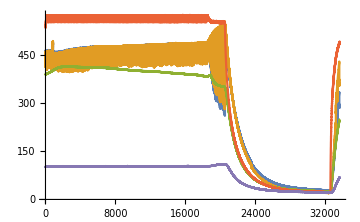

```mathematica
ListPlot[e2,Joined->True]
```